```mathematica
j=ⅈ;
uzel1=0==iZD+iR;
uzel2=iR==iC+iR2;
odpor=iR==(u1-u2)/R;
zdroj=u1==uZ;
cond=iC==u2*10^4*j*c;
odpor2=iR2==u2/R2;
R=10000;
c=10^-8;
R2=10000;


uZ=12.5*ⅇ^(1.2*j);
```

```mathematica
VsechnyRovnice={uzel1,uzel2,odpor,cond,zdroj,odpor2};
```

```mathematica
Reseni=Solve[VsechnyRovnice,{iZD,iR,iC,u1,u2,iR2}]
```

{{iZD→-0.0000387585-0.000789619 ⅈ,iR→0.0000387585+0.000789619 ⅈ,iC→-0.00037543+0.000414189 ⅈ,u1→4.52947+11.6505 ⅈ,u2→4.14189+3.7543 ⅈ,iR2→0.000414189+0.00037543 ⅈ}}

{4.14189+3.7543 ⅈ}

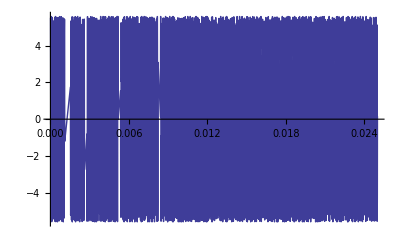

```mathematica
u2f=u2/.Reseni
u2t[t_]:=Abs[u2f]*Sin[10^5*t+Arg[u2f]];
Plot[u2t[t],{t,0.0000100,0.025}]
```